Pumping power is -10.11dBm.

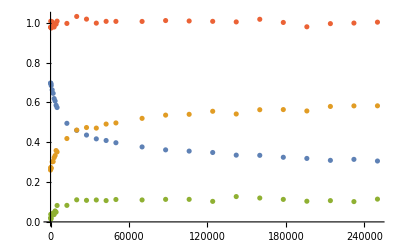

```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"optimal_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 5.dBm.

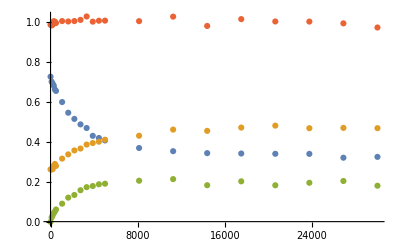

```mathematica
file=path<>"high_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is -25.dBm.

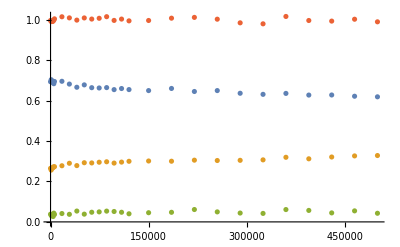

```mathematica
file=path<>"low_power_transient_population.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

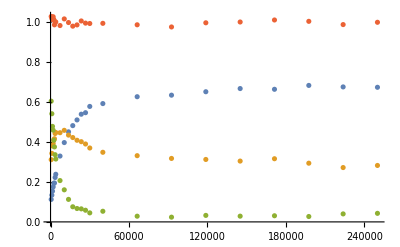

```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

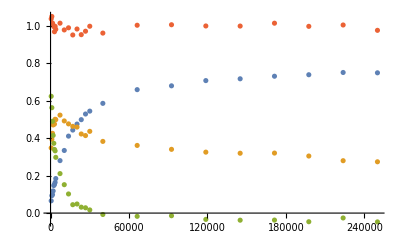

```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay_0122.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

{1200.,2960.,4720.,6480.,8240.,10000.,16000.,22000.,28000.,34000.,40000.,82000.,124000.,166000.,208000.,250000.}

Pumping power is 25.dBm.

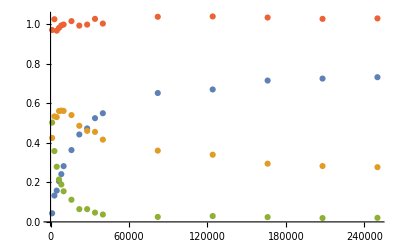

```mathematica
path="C:\\SC Lab\\GitHubRepositories\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
file=path<>"02_pi_pulse_decay_interleaved.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
Time = data["/time"]
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{Time,P0}];
P1toPlot=Transpose[{Time,P1}];
P2toPlot=Transpose[{Time,P2}];
PSumtoPlot=Transpose[{Time,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

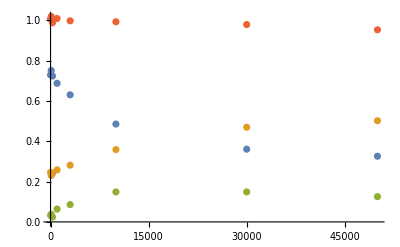

```mathematica
file=path<>"transient_P2_P1_interleaved.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

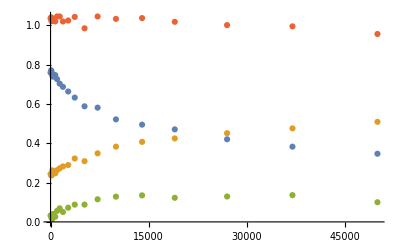

```mathematica
file=path<>"transient_P2_P1_interleaved_more_points.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 25.dBm.

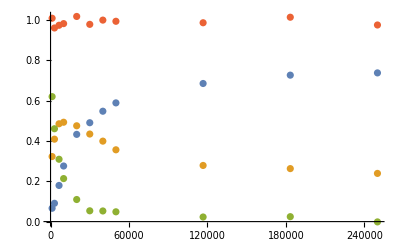

```mathematica
file=path<>"t1_population_2020-02-10-04-07-55.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

Pumping power is 20.dBm.

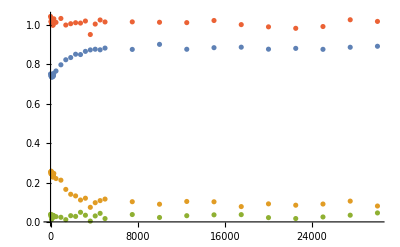

```mathematica
file=path<>"transient_1_3_pumping.hdf5";
data=Import[file, "Data"];
TransientPower = data["/power"];
PumpingTime = data["/time"];
Population=data["/y"];
P0=Population[[1]];
P1=Population[[2]];
P2=Population[[3]];
P0toPlot=Transpose[{PumpingTime,P0}];
P1toPlot=Transpose[{PumpingTime,P1}];
P2toPlot=Transpose[{PumpingTime,P2}];
PSumtoPlot=Transpose[{PumpingTime,P0+P1+P2}];
Text["Pumping power is "<>ToString[TransientPower]<>"dBm."]
Show[ListPlot[{P0toPlot,P1toPlot,P2toPlot,PSumtoPlot}]]
```

```mathematica
P2
```

{0.038376,0.0300171,0.0373392,0.0123522,0.0287849,0.0231915,0.025288,0.0336533,0.0222356,0.0316523,0.0306356,0.0267344,0.0234812,0.0112927,0.0315554,0.0279772,0.0488516,0.0338635,0.00401248,0.0303132,0.0434585,0.0168568,0.0373791,0.0224651,0.0314867,0.0358717,0.0369219,0.0217648,0.0170392,0.0250883,0.0340577,0.0455829}

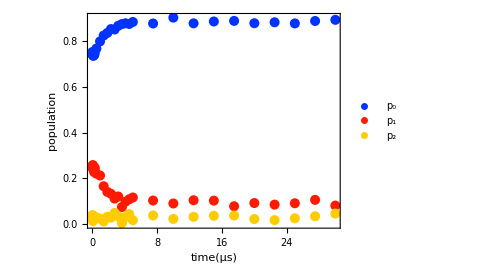

```mathematica
PtSize=0.02;
Time=PumpingTime/1000;
g=Show[ListPlot[{Transpose@{Time,P0},Transpose@{Time,P1},Transpose@{Time,P2}}, PlotStyle->{{PointSize[PtSize],RGBColor[0,0.2,1]},{PointSize[PtSize],RGBColor[1,0.1,0]},{PointSize[PtSize],RGBColor[1,0.8,0]}},PlotLegends->Placed[PointLegend[{"p_0","p_1","p_2"},LegendFunction->(Framed[#]&),LabelStyle->{FontFamily->"Times New Roman",Black,14}],{Right,Center}]]
,Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75,FrameLabel->{Style["time(μs)",Black,18,FontFamily->"Times New Roman"],Style["population",Black,18,FontFamily->"Times New Roman"]}]
```

```mathematica
Export[path<>"13pumping.pdf",g]
```

C:\SC Lab\GitHubRepositories\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\13pumping.pdf